```mathematica
ClearAll["Global`*"];

(* import functions *)
Get["/Users/csfloyd/Dropbox/Projects/CoupledLearningMarkov/Mathematica/CLFunctions.m"];
```

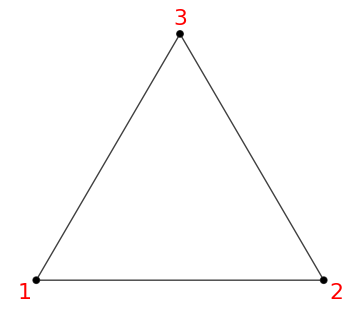

```mathematica
SeedRandom[36];

nNodes = 3;


g = CreateFullGraph[nNodes];

(*Extract information from the input graph*)
nNodes=VertexCount[g];
nEdges=EdgeCount[g];
adjMat=AdjacencyMatrix[g];
edges=EdgeList[g];

vCoords = {{-1,-1},{-1,1},{1,1},{1,-1}};
Graph[g,VertexLabels->"Name",VertexStyle->Black,EdgeStyle->Directive[Black,Thick,Opacity[0.75]],ImageSize->Medium,VertexLabelStyle->Directive[Black,22,Red]]
```

```mathematica
WijFromParams[g_,edges_,nEdges_, nNodes_,adjMat_,EjList_,BijList_,FijList_]:=Module[{WijList,WjiList,n1,n2,Bij,Fij,Ei,Ej,Wij,Wji},

(*Initialize the weight matrix*)
WijList = {};
WjiList = {};
(*Populate the weight matrix using given formulas*)
Do[n1=edges[[e]][[1]];
n2=edges[[e]][[2]];
Bij=BijList[[e]];
Fij=FijList[[e]];
Ei=EjList[[n1]];
Ej=EjList[[n2]];
Wij=Exp[-Bij+Ej+Fij/2];

AppendTo[WijList, Wij];
Wji=Exp[-Bij+Ei-Fij/2];
AppendTo[WjiList, Wji];
,{e,1,nEdges}];


(*Return the resulting weight matrix*)
{WijList, WjiList}];
```

```mathematica
EjList = Range[0,nNodes-1];
FijList =Range[0,nEdges-1];
BijList = Range[0,nEdges-1];

{EjListSym,pkListSym,BijListSym,FijListSym} = CreateSymblolicLists[nNodes,nEdges,edges];
{WijListP,WjiListP}=WijFromParams[g,edges,nEdges,nNodes,adjMat,EjListSym,BijListSym,FijListSym];
{WijListSym, WjiListSym} = CreateSymblolicListsWij[nNodes,nEdges,edges];
WijMatSymP=UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjListSym, BijListSym,FijListSym];
WijMatSym=UpdateWeightMatrixWij[g,edges,nEdges, nNodes,adjMat, WijListSym, WjiListSym];


WijMat= UpdateWeightMatrix[g,edges,nEdges, nNodes,adjMat, EjList, BijList,FijList];
evals = Join[
Table[EjListSym[[k]]->EjList[[k]],{k,1,nNodes}],
Table[BijListSym[[k]]->BijList[[k]],{k,1,nEdges}],
Table[FijListSym[[k]]->FijList[[k]],{k,1,nEdges}]]

evalsW = Join[
Table[WijListSym[[k]]->WijListP[[k]]/.evals,{k,1,nEdges}],
Table[WjiListSym[[k]]->WjiListP[[k]]/.evals,{k,1,nEdges}]]
```

{E1→0,E2→1,E3→2,B12→0,B13→1,B23→2,F12→0,F13→1,F23→2}

{W12→ⅇ,W13→ⅇ^(3/2),W23→ⅇ,W21→1,W31→1/ⅇ^(3/2),W32→1/ⅇ^2}

```mathematica
WijMat//N//MatrixForm
```

(-1.22313 | 2.71828 | 4.48169
1. | -2.85362 | 2.71828
0.22313 | 0.135335 | -7.19997)

```mathematica
EjList={0,1,2};
BijList = {3,4,5};
FijList = {6,7,8};
evals = Join[
Table[EjListSym[[k]]->EjList[[k]],{k,1,nNodes}],
Table[BijListSym[[k]]->BijList[[k]],{k,1,nEdges}],
Table[FijListSym[[k]]->FijList[[k]],{k,1,nEdges}]]
```

{E1→0,E2→1,E3→2,B12→3,B13→4,B23→5,F12→6,F13→7,F23→8}

```mathematica
piSymP = GetStationaryDistributionTrees[g, nNodes, WijMatSymP]/.evals//N
```

{0.998936,0.000987571,0.0000767818}

```mathematica
inputInds = {{1,2}};
signs = {1,1};
(*inputInds = {{1}};
signs = {1};*)
repBool = False;
inputs = {-5};

WijMatPre=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListSym, BijListSym, FijListSym,repBool]
piSymP = GetStationaryDistributionTrees[g, nNodes, WijMatPre];
piSymP/.evals//N
Grad[piSymP,EjListSym]/.evals//N
Grad[piSymP,BijListSym]/.evals//N
Grad[piSymP,FijListSym]/.evals//N
```

{{-ⅇ^(-B12+E1+(5-F12)/2)-ⅇ^(-B13+E1+(5-F13)/2),ⅇ^(-B12+E2+1/2 (-5+F12)),ⅇ^(-B13+E3+1/2 (-5+F13))},{ⅇ^(-B12+E1+(5-F12)/2),-ⅇ^(-B12+E2+1/2 (-5+F12))-ⅇ^(-B23+E2-F23/2),ⅇ^(-B23+E3+F23/2)},{ⅇ^(-B13+E1+(5-F13)/2),ⅇ^(-B23+E2-F23/2),-ⅇ^(-B13+E3+1/2 (-5+F13))-ⅇ^(-B23+E3+F23/2)}}

{0.859029,0.13908,0.00189062}

{{-0.121098,0.119474,0.00162409},{0.119474,-0.119737,0.000262948},{0.00162409,0.000262948,-0.00188704}}

{{-0.0196045,0.0186851,0.000919405},{0.0196452,-0.0170739,-0.00257126},{-0.0000406667,-0.00161119,0.00165186}}

{{0.109663,0.0118945,-0.000468126},{-0.109891,-0.0108688,0.00130919},{0.00022748,-0.00102565,-0.000841064}}

```mathematica
EjListSymB = EjListSym;
EjListSymA = EjListSym;
Do[
EjListSymA[[n]]=Symbol[ToString[EjListSym[[n]]]<>"A"];
EjListSymB[[n]]=Symbol[ToString[EjListSym[[n]]]<>"B"]
,{n,1,Length[EjListSym]}]

BijListSymB = BijListSym;
BijListSymA = BijListSym;
Do[
BijListSymA[[n]]=Symbol[ToString[BijListSym[[n]]]<>"A"];
BijListSymB[[n]]=Symbol[ToString[BijListSym[[n]]]<>"B"]
,{n,1,Length[BijListSym]}]

FijListSymB = FijListSym;
FijListSymA = FijListSym;
Do[
FijListSymA[[n]]=Symbol[ToString[FijListSym[[n]]]<>"A"];
FijListSymB[[n]]=Symbol[ToString[FijListSym[[n]]]<>"B"]
,{n,1,Length[FijListSym]}]

EjListA={0,1,2};
BijListA = {3,4,5};
FijListA = {6,7,8};
evalsA = Join[
Table[EjListSymA[[k]]->EjListA[[k]],{k,1,nNodes}],
Table[BijListSymA[[k]]->BijListA[[k]],{k,1,nEdges}],
Table[FijListSymA[[k]]->FijListA[[k]],{k,1,nEdges}]];

EjListB={0,1,2};
BijListB = {3,4,5};
FijListB = {6,7,8};
evalsB = Join[
Table[EjListSymB[[k]]->EjListB[[k]],{k,1,nNodes}],
Table[BijListSymB[[k]]->BijListB[[k]],{k,1,nEdges}],
Table[FijListSymB[[k]]->FijListB[[k]],{k,1,nEdges}]];
```

```mathematica
inputInds = {{1,2}};
signs = {1,1};
repBool = False;
inputs = {-5};

WijMatPreA=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListSymA, BijListSymA, FijListSymA,repBool];
piSymPA= GetStationaryDistributionTrees[g, nNodes, WijMatPreA];


aval = -5;
bval = -0.5;
evalsV = {a->aval, b->bval};


Amat ={{a}};
bvec ={b};
fev= Amat.{piSymPA[[1]]} + bvec;
newInput = Amat.{piSymPA[[1]]} + bvec;
evalsV = {a->aval, b->bval};

(*newInput={f};*)
WijMatPreB = MapInputToWijMat[newInput,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListSymB, BijListSymB, FijListSymB,repBool];
piSymPB= GetStationaryDistributionTrees[g, nNodes, WijMatPreB];
piSymPA/.evalsA/.evalsB//N
piSymPB/.evalsA/.evalsB/.evalsV//N

Grad[piSymPB,EjListSymA]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,BijListSymA]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,FijListSymA]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,EjListSymB]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,BijListSymB]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,FijListSymB]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,{a,b}]/.evalsA/.evalsB/.evalsV//N//MatrixForm
```

{0.859029,0.13908,0.00189062}

{0.882146,0.116125,0.00172886}

(0.0632077 | -0.06236 | -0.000847703
-0.062736 | 0.0618947 | 0.000841378
-0.000471624 | 0.000465299 | 6.32513×10^-6)

(0.0102327 | -0.00975278 | -0.000479887
-0.0101563 | 0.00968001 | 0.000476307
-0.000076351 | 0.0000727703 | 3.58068×10^-6)

(-0.0572392 | -0.00620838 | 0.00024434
0.0568121 | 0.00616205 | -0.000242517
0.00042709 | 0.0000463238 | -1.82314×10^-6)

(-0.103964 | 0.102439 | 0.00152511
0.102439 | -0.10264 | 0.000200764
0.00152511 | 0.000200764 | -0.00172587)

(-0.0166306 | 0.0157775 | 0.000853089
0.0166612 | -0.0143157 | -0.00234548
-0.0000305702 | -0.00146182 | 0.00149239)

(0.0941168 | 0.0102741 | -0.000433675
-0.0942898 | -0.00932216 | 0.00119234
0.000173005 | -0.000951916 | -0.00075867)

(0.0896748 | 0.104391
-0.0890057 | -0.103612
-0.000669108 | -0.000778912)

```mathematica
fv=Amat.{piSymPA[[1]]} + bvec/.evalsA/.evalsB/.evalsV;
Grad[piSymPB,{f}]/.evalsA/.evalsB/.evalsV/.{f->fv}//N
```

{{{0.104391}},{{-0.103612}},{{-0.000778912}}}

```mathematica
EjListSymB = EjListSym;
EjListSymA = EjListSym;
Do[
EjListSymA[[n]]=Symbol[ToString[EjListSym[[n]]]<>"A"];
EjListSymB[[n]]=Symbol[ToString[EjListSym[[n]]]<>"B"]
,{n,1,Length[EjListSym]}]

BijListSymB = BijListSym;
BijListSymA = BijListSym;
Do[
BijListSymA[[n]]=Symbol[ToString[BijListSym[[n]]]<>"A"];
BijListSymB[[n]]=Symbol[ToString[BijListSym[[n]]]<>"B"]
,{n,1,Length[BijListSym]}]

FijListSymB = FijListSym;
FijListSymA = FijListSym;
Do[
FijListSymA[[n]]=Symbol[ToString[FijListSym[[n]]]<>"A"];
FijListSymB[[n]]=Symbol[ToString[FijListSym[[n]]]<>"B"]
,{n,1,Length[FijListSym]}]

EjListA={0,1,2};
BijListA = {3,4,5};
FijListA = {6,7,8};
evalsA = Join[
Table[EjListSymA[[k]]->EjListA[[k]],{k,1,nNodes}],
Table[BijListSymA[[k]]->BijListA[[k]],{k,1,nEdges}],
Table[FijListSymA[[k]]->FijListA[[k]],{k,1,nEdges}]];

EjListB={0,1,2};
BijListB = {3,4,5};
FijListB = {6,7,8};
evalsB = Join[
Table[EjListSymB[[k]]->EjListB[[k]],{k,1,nNodes}],
Table[BijListSymB[[k]]->BijListB[[k]],{k,1,nEdges}],
Table[FijListSymB[[k]]->FijListB[[k]],{k,1,nEdges}]];
```

```mathematica
inputInds = {{1,2}};
signs = {1,1};
repBool = False;
inputs = {-5};

WijMatPreA=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListSymA, BijListSymA, FijListSymA,repBool];
piSymPA= GetStationaryDistributionTrees[g, nNodes, WijMatPreA];


aval = -5;
bval = -0.5;
evalsV = {a->aval, b->bval};


Amat ={{a}};
bvec ={b};
fev= Amat.{piSymPA[[1]]} + bvec;
newInput = Amat.{piSymPA[[1]]} + bvec;
evalsV = {a->aval, b->bval};

(*newInput={f};*)
WijMatPreB = MapInputToWijMat[newInput,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListSymB, BijListSymB, FijListSymB,repBool];
piSymPB= GetStationaryDistributionTrees[g, nNodes, WijMatPreB];
piSymPA/.evalsA/.evalsB//N
piSymPB/.evalsA/.evalsB/.evalsV//N

Grad[piSymPB,EjListSymA]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,BijListSymA]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,FijListSymA]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,EjListSymB]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,BijListSymB]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,FijListSymB]/.evalsA/.evalsB/.evalsV//N//MatrixForm
Grad[piSymPB,{a,b}]/.evalsA/.evalsB/.evalsV//N//MatrixForm
```

{0.859029,0.13908,0.00189062}

{0.882146,0.116125,0.00172886}

(0.0632077 | -0.06236 | -0.000847703
-0.062736 | 0.0618947 | 0.000841378
-0.000471624 | 0.000465299 | 6.32513×10^-6)

(0.0102327 | -0.00975278 | -0.000479887
-0.0101563 | 0.00968001 | 0.000476307
-0.000076351 | 0.0000727703 | 3.58068×10^-6)

(-0.0572392 | -0.00620838 | 0.00024434
0.0568121 | 0.00616205 | -0.000242517
0.00042709 | 0.0000463238 | -1.82314×10^-6)

(-0.103964 | 0.102439 | 0.00152511
0.102439 | -0.10264 | 0.000200764
0.00152511 | 0.000200764 | -0.00172587)

(-0.0166306 | 0.0157775 | 0.000853089
0.0166612 | -0.0143157 | -0.00234548
-0.0000305702 | -0.00146182 | 0.00149239)

(0.0941168 | 0.0102741 | -0.000433675
-0.0942898 | -0.00932216 | 0.00119234
0.000173005 | -0.000951916 | -0.00075867)

(0.0896748 | 0.104391
-0.0890057 | -0.103612
-0.000669108 | -0.000778912)

```mathematica
(*Extend symbol lists to include layer C*)EjListSymC=EjListSym;
EjListSymA=EjListSym;
EjListSymB=EjListSym;
Do[EjListSymA[[n]]=Symbol[ToString[EjListSym[[n]]]<>"A"];
EjListSymB[[n]]=Symbol[ToString[EjListSym[[n]]]<>"B"];
EjListSymC[[n]]=Symbol[ToString[EjListSym[[n]]]<>"C"];,{n,1,Length[EjListSym]}];

BijListSymC=BijListSym;
BijListSymA=BijListSym;
BijListSymB=BijListSym;
Do[BijListSymA[[n]]=Symbol[ToString[BijListSym[[n]]]<>"A"];
BijListSymB[[n]]=Symbol[ToString[BijListSym[[n]]]<>"B"];
BijListSymC[[n]]=Symbol[ToString[BijListSym[[n]]]<>"C"];,{n,1,Length[BijListSym]}];

FijListSymC=FijListSym;
FijListSymA=FijListSym;
FijListSymB=FijListSym;
Do[FijListSymA[[n]]=Symbol[ToString[FijListSym[[n]]]<>"A"];
FijListSymB[[n]]=Symbol[ToString[FijListSym[[n]]]<>"B"];
FijListSymC[[n]]=Symbol[ToString[FijListSym[[n]]]<>"C"];,{n,1,Length[FijListSym]}];

(*Evaluation lists for A,B,and C*)
EjListA={0,1,2};
BijListA={3,4,5};
FijListA={6,7,8};
evalsA=Join[Table[EjListSymA[[k]]->EjListA[[k]],{k,1,nNodes}],Table[BijListSymA[[k]]->BijListA[[k]],{k,1,nEdges}],Table[FijListSymA[[k]]->FijListA[[k]],{k,1,nEdges}]];

EjListB={0,1,2};
BijListB={3,4,5};
FijListB={6,7,8};
evalsB=Join[Table[EjListSymB[[k]]->EjListB[[k]],{k,1,nNodes}],Table[BijListSymB[[k]]->BijListB[[k]],{k,1,nEdges}],Table[FijListSymB[[k]]->FijListB[[k]],{k,1,nEdges}]];

EjListC={0,1,2};
BijListC={3,4,5};
FijListC={6,7,8};
evalsC=Join[Table[EjListSymC[[k]]->EjListC[[k]],{k,1,nNodes}],Table[BijListSymC[[k]]->BijListC[[k]],{k,1,nEdges}],Table[FijListSymC[[k]]->FijListC[[k]],{k,1,nEdges}]];
```

```mathematica
inputInds = {{1,2}};
signs = {1,1};
repBool = False;
inputs = {-5};

WijMatPreA=MapInputToWijMat[inputs,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListSymA, BijListSymA, FijListSymA,repBool];
piSymPA= GetStationaryDistributionTrees[g, nNodes, WijMatPreA];

aval = -5;
bval = -0.5;


Amat1 ={{a1}};
bvec1 ={b1};
fev1= Amat1.{piSymPA[[1]]} + bvec1;
newInput1= Amat1.{piSymPA[[1]]} + bvec1;
evalsV1 = {a1->aval, b1->bval};

(*newInput={f};*)
WijMatPreB = MapInputToWijMat[newInput1,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListSymB, BijListSymB, FijListSymB,repBool];
piSymPB= GetStationaryDistributionTrees[g, nNodes, WijMatPreB];


Amat2 ={{a2}};
bvec2 ={b2};
fev2= Amat2.{piSymPB[[1]]} + bvec2;
newInput2 = Amat2.{piSymPB[[1]]} + bvec2;
evalsV2 = {a2->aval, b2->bval};


WijMatPreC= MapInputToWijMat[newInput2,inputInds,signs,g,edges,nEdges,nNodes,adjMat,EjListSymC, BijListSymC, FijListSymC,repBool];
piSymPC= GetStationaryDistributionTrees[g, nNodes, WijMatPreC];

piSymPA/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N
piSymPB/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N
piSymPC/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N
(*piSymPC/.evalsA/.evalsB/.evalsC/.evalsV1//N*)

Grad[piSymPC,EjListSymA]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
Grad[piSymPC,BijListSymA]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
Grad[piSymPC,FijListSymA]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
Grad[piSymPC,EjListSymB]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
Grad[piSymPC,BijListSymB]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
Grad[piSymPC,FijListSymB]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
Grad[piSymPC,EjListSymC]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
Grad[piSymPC,BijListSymC]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
Grad[piSymPC,FijListSymC]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
Grad[piSymPC,{a1,b1}]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
Grad[piSymPC,{a2,b2}]/.evalsA/.evalsB/.evalsC/.evalsV1/.evalsV2//N//MatrixForm
```

{0.859029,0.13908,0.00189062}

{0.882146,0.116125,0.00172886}

{0.869536,0.128644,0.00181965}

(-0.0359932 | 0.0355105 | 0.000482719
0.0357431 | -0.0352637 | -0.000479365
0.000250106 | -0.000246752 | -3.35427×10^-6)

(-0.00582692 | 0.00555365 | 0.000273269
0.00578643 | -0.00551506 | -0.00027137
0.0000404896 | -0.0000385907 | -1.89886×10^-6)

(0.0325945 | 0.00353532 | -0.000139138
-0.032368 | -0.00351075 | 0.000138171
-0.00022649 | -0.0000245659 | 9.66828×10^-7)

(0.0592018 | -0.0583333 | -0.000868462
-0.0587904 | 0.057928 | 0.000862427
-0.000411376 | 0.000405341 | 6.03469×10^-6)

(0.00947018 | -0.0089844 | -0.000485786
-0.00940438 | 0.00892197 | 0.00048241
-0.0000658055 | 0.0000624299 | 3.37558×10^-6)

(-0.0535942 | -0.00585051 | 0.000246953
0.0532218 | 0.00580985 | -0.000245237
0.00037241 | 0.0000406534 | -1.71601×10^-6)

(-0.113443 | 0.111861 | 0.00158225
0.111861 | -0.112095 | 0.000234087
0.00158225 | 0.000234087 | -0.00181634)

(-0.0182722 | 0.017381 | 0.000891188
0.0183082 | -0.0158352 | -0.00247293
-0.000035966 | -0.00154578 | 0.00158174)

(0.102717 | 0.0111718 | -0.000453438
-0.102919 | -0.0101782 | 0.00125823
0.000202183 | -0.000993561 | -0.000804793)

(-0.0510647 | -0.0594447
0.0507099 | 0.0590316
0.000354833 | 0.000413063)

(0.100466 | 0.113889
-0.0997683 | -0.113097
-0.000698112 | -0.000791379)